# Buscando padrões em números primos

```mathematica
(* Lista dos primeiros n primos. *)
t[n_]:=Table[Prime[i],{i,1,n}]
(* N-ésima derivada discreta de uma lista arbitrária. *)
DiffL[difs_,l_]:=If[difs==0,l,Differences[DiffL[difs-1,l]]]
(* N-ésima derivada discreta da lista dos primeiros n primeros. *)
DiffP[difs_,n_]:=DiffL[difs,t[n]]
```

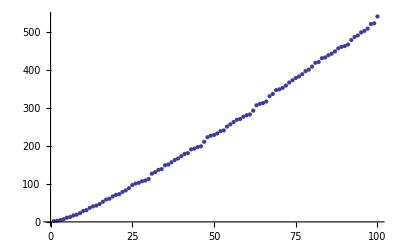
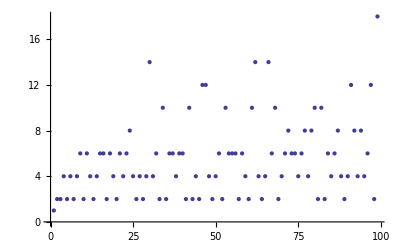
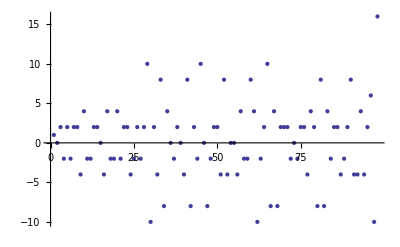
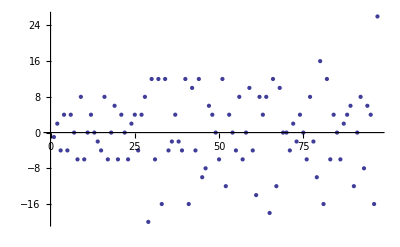
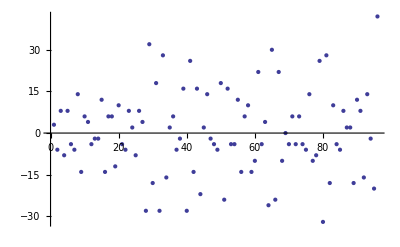
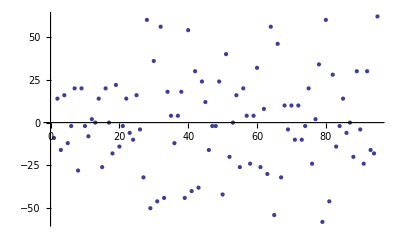

```mathematica
(* 1-6a derivada discreta da lista dos 50 primeiros primos. *)
Table[ListPlot[DiffP[d, 100]],{d,0,5}]
```

```mathematica
(* Em `d2', busca quais são os índices cujos valores são 0, i.e. primos cuja diferença é 2. *)
d2=DiffP[2,2000];
pp2=Position[d2,0];
p2=Flatten[pp2]
Table[DiffL[i,p2],{i,1,5}]//TableForm
```

{2,15,36,39,46,54,55,73,102,107,110,118,129,160,164,184,187,194,199,218,239,271,272,291,339,358,387,419,426,464,465,508,520,553,599,605,621,629,633,667,682,683,702,709,710,733,761,791,813,821,822,829,830,882,896,952,962,988,990,1020,1085,1090,1161,1173,1217,1256,1293,1299,1318,1365,1376,1386,1407,1414,1425,1429,1491,1498,1502,1510,1511,1530,1544,1553,1567,1594,1595,1702,1726,1727,1770,1773,1788,1806,1838,1842,1843,1853,1854,1873,1884,1903,1910,1917,1921,1938,1953,1958,1966,1991}

13 | 21 | 3 | 7 | 8 | 1 | 18 | 29 | 5 | 3 | 8 | 11 | 31 | 4 | 20 | 3 | 7 | 5 | 19 | 21 | 32 | 1 | 19 | 48 | 19 | 29 | 32 | 7 | 38 | 1 | 43 | 12 | 33 | 46 | 6 | 16 | 8 | 4 | 34 | 15 | 1 | 19 | 7 | 1 | 23 | 28 | 30 | 22 | 8 | 1 | 7 | 1 | 52 | 14 | 56 | 10 | 26 | 2 | 30 | 65 | 5 | 71 | 12 | 44 | 39 | 37 | 6 | 19 | 47 | 11 | 10 | 21 | 7 | 11 | 4 | 62 | 7 | 4 | 8 | 1 | 19 | 14 | 9 | 14 | 27 | 1 | 107 | 24 | 1 | 43 | 3 | 15 | 18 | 32 | 4 | 1 | 10 | 1 | 19 | 11 | 19 | 7 | 7 | 4 | 17 | 15 | 5 | 8 | 25
8 | -18 | 4 | 1 | -7 | 17 | 11 | -24 | -2 | 5 | 3 | 20 | -27 | 16 | -17 | 4 | -2 | 14 | 2 | 11 | -31 | 18 | 29 | -29 | 10 | 3 | -25 | 31 | -37 | 42 | -31 | 21 | 13 | -40 | 10 | -8 | -4 | 30 | -19 | -14 | 18 | -12 | -6 | 22 | 5 | 2 | -8 | -14 | -7 | 6 | -6 | 51 | -38 | 42 | -46 | 16 | -24 | 28 | 35 | -60 | 66 | -59 | 32 | -5 | -2 | -31 | 13 | 28 | -36 | -1 | 11 | -14 | 4 | -7 | 58 | -55 | -3 | 4 | -7 | 18 | -5 | -5 | 5 | 13 | -26 | 106 | -83 | -23 | 42 | -40 | 12 | 3 | 14 | -28 | -3 | 9 | -9 | 18 | -8 | 8 | -12 | 0 | -3 | 13 | -2 | -10 | 3 | 17 | 
-26 | 22 | -3 | -8 | 24 | -6 | -35 | 22 | 7 | -2 | 17 | -47 | 43 | -33 | 21 | -6 | 16 | -12 | 9 | -42 | 49 | 11 | -58 | 39 | -7 | -28 | 56 | -68 | 79 | -73 | 52 | -8 | -53 | 50 | -18 | 4 | 34 | -49 | 5 | 32 | -30 | 6 | 28 | -17 | -3 | -10 | -6 | 7 | 13 | -12 | 57 | -89 | 80 | -88 | 62 | -40 | 52 | 7 | -95 | 126 | -125 | 91 | -37 | 3 | -29 | 44 | 15 | -64 | 35 | 12 | -25 | 18 | -11 | 65 | -113 | 52 | 7 | -11 | 25 | -23 | 0 | 10 | 8 | -39 | 132 | -189 | 60 | 65 | -82 | 52 | -9 | 11 | -42 | 25 | 12 | -18 | 27 | -26 | 16 | -20 | 12 | -3 | 16 | -15 | -8 | 13 | 14 |  | 
48 | -25 | -5 | 32 | -30 | -29 | 57 | -15 | -9 | 19 | -64 | 90 | -76 | 54 | -27 | 22 | -28 | 21 | -51 | 91 | -38 | -69 | 97 | -46 | -21 | 84 | -124 | 147 | -152 | 125 | -60 | -45 | 103 | -68 | 22 | 30 | -83 | 54 | 27 | -62 | 36 | 22 | -45 | 14 | -7 | 4 | 13 | 6 | -25 | 69 | -146 | 169 | -168 | 150 | -102 | 92 | -45 | -102 | 221 | -251 | 216 | -128 | 40 | -32 | 73 | -29 | -79 | 99 | -23 | -37 | 43 | -29 | 76 | -178 | 165 | -45 | -18 | 36 | -48 | 23 | 10 | -2 | -47 | 171 | -321 | 249 | 5 | -147 | 134 | -61 | 20 | -53 | 67 | -13 | -30 | 45 | -53 | 42 | -36 | 32 | -15 | 19 | -31 | 7 | 21 | 1 |  |  | 
-73 | 20 | 37 | -62 | 1 | 86 | -72 | 6 | 28 | -83 | 154 | -166 | 130 | -81 | 49 | -50 | 49 | -72 | 142 | -129 | -31 | 166 | -143 | 25 | 105 | -208 | 271 | -299 | 277 | -185 | 15 | 148 | -171 | 90 | 8 | -113 | 137 | -27 | -89 | 98 | -14 | -67 | 59 | -21 | 11 | 9 | -7 | -31 | 94 | -215 | 315 | -337 | 318 | -252 | 194 | -137 | -57 | 323 | -472 | 467 | -344 | 168 | -72 | 105 | -102 | -50 | 178 | -122 | -14 | 80 | -72 | 105 | -254 | 343 | -210 | 27 | 54 | -84 | 71 | -13 | -12 | -45 | 218 | -492 | 570 | -244 | -152 | 281 | -195 | 81 | -73 | 120 | -80 | -17 | 75 | -98 | 95 | -78 | 68 | -47 | 34 | -50 | 38 | 14 | -20 |  |  |  |